```mathematica
a=Import["C:\\OSU\\Research\\repo\\empirical-cov-experiments\\individual_experiments\\fastica-07-15-2015\\Figures\\data.mat","Data"];
```

```mathematica
a=Partition[Flatten[a],37];
```

```mathematica
Dimensions[a]
```

{74,37}

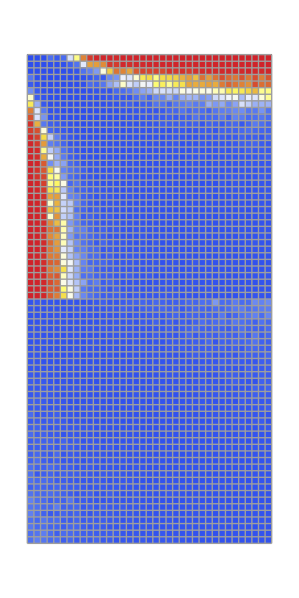

```mathematica
S1=ArrayPlot[a,PlotRange->All,Mesh->All,ColorFunctionScaling->True,ColorFunction->"TemperatureMap"]
```

```mathematica
Export["C:\\OSU\\Research\\repo\\empirical-cov-experiments\\individual_experiments\\fastica-07-15-2015\\Figures\\exponents.png",S1,"PNG"]
```

C:\OSU\Research\repo\empirical-cov-experiments\individual_experiments\fastica-07-15-2015\Figures\exponents.png

```mathematica
Manipulate[
ArrayPlot[Map[If[#1>t,t,#1]&,a,{2}],PlotRange->All,Mesh->All,ColorFunctionScaling->True,ColorFunction->"TemperatureMap"],
{{t,.03},0,.5}]
```

```mathematica
b=a[[1;;37]]-a[[38;;74]];
```

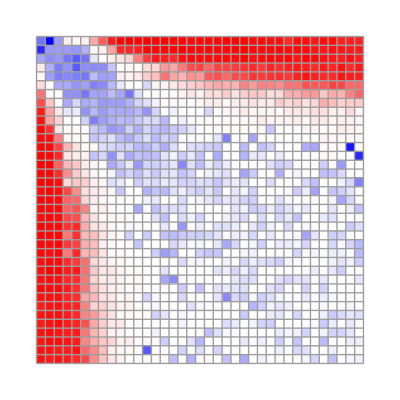

```mathematica
With[{t=100},
ArrayPlot[Map[If[#1>t,t,#1]&,b,{2}],PlotRange->All,Mesh->All,ColorFunctionScaling->False,ColorFunction->(Blend[{{Min[b],Blue}, {0,White}, {Max[b],Red}}, #1] &)
]
]
```

```mathematica
Export["C:\\OSU\\Research\\repo\\empirical-cov-experiments\\individual_experiments\\fastica-07-15-2015\\Figures\\undamp_vs_damp.png",%128,"PNG"]
```

C:\OSU\Research\repo\empirical-cov-experiments\individual_experiments\fastica-07-15-2015\Figures\undamp_vs_damp.png